```mathematica
(*
up to down:hadron[Xi Lambda proton phi Omega];
left to right:centrality[05 1020 2030 3040 4060];
N_1~5:[7.7 11.5 19.6 27 39].
*)
N1={{11.4541, 5.7481 ,3.3974 ,1.6814 },{221.7333 ,121.6216 ,70.6142,37.8018 } ,{937.5287 ,566.2210 ,368.7218 ,238.3657 },{6.2428 ,3.8052 ,2.5086 ,1.5196 } ,{0 ,0 ,0 ,0 }};
N2={{11.1153, 6.1330, 3.3806, 1.8493} ,{179.3339, 101.5673, 62.7649, 33.8882},{635.8842, 366.4048 ,241.2366, 152.4688 },{8.0395, 5.6268, 3.3273, 1.8992 },{0.5799, 0, 0, 0}};

N3={{10.9911 ,5.9457 ,3.5640 ,1.9261},{130.7303 ,76.8028 ,47.5971, 26.7954},{395.3207 ,245.3865 ,153.9598, 92.3687 },{9.6833 ,6.4485 ,4.0067 ,2.6322 },{ 0.8011 ,0.4465, 0.1766, 0.0394}};

N4={{9.3405, 5.3155, 3.2140, 1.7473 },{ 109.6440 ,67.6402 ,41.5905, 25.1997},{313.4100 ,195.5461 ,128.5665, 81.0629 },{10.7767 ,7.0331 ,4.6008, 2.6347},{0.7552 ,0.4353 ,0.2105, 0.0455}};

N5={{8.0985, 4.8723, 2.8916 ,1.6647},{ 95.5787, 56.6530, 37.1188, 22.6504 },{231.2633, 147.4718, 99.9727 ,63.9899 },{10.2722 ,7.2200 ,4.7706 ,3.0662 },{0.6946, 0.4129 ,0.2032, 0.0434}};
```

```mathematica
(*
left to right:[05 1020 2030 3040 4050 5060];39GeV
*)
Npart={342,230,162,111};
```

```mathematica
A1h[sqrts_]:=A0h*Sqrt[sqrts]^-bh(*sqrts in TeV*);
Ah[sqrts_,Npart_]:=A1h[sqrts]*Npart^ah;ah=1.35;(*a universal scaling exponent ah for Npart>60*)
A0hbh={{proton,0.035,0.315},{lambda,0.0191,0.245},{Xi,0.0016,0.175},{Omega,1.7507*^-4,0.105}};
Npart={{Xi,0.011TeV,20.2,58.4,109.9,160.2,226.2,290.4,337.4}，{lambda,0.039TeV,20.0,59.2,111.4,162.4,229.8,293.9,341.7}};
```

```mathematica
(*proton*)
A1hp={
N1[[3,;;]]/((Npart^1.35)),
N2[[3,;;]]/((Npart^1.35)),N3[[3,;;]]/((Npart^1.35)),N4[[3,;;]]/((Npart^1.35)),
N5[[3,;;]]/((Npart^1.35))}
```

{{0.355672,0.366989,0.383578,0.413102},{0.241236,0.237481,0.250956,0.264238},{0.149973,0.159044,0.160163,0.160081},{0.118899,0.126741,0.133747,0.140487},{0.0877347,0.0955821,0.104001,0.110898}}

```mathematica
A1hsp={{7.7*^-3,Mean[A1hp[[1]]]},
{11.5*^-3,Mean[A1hp[[2]]]},
{19.6*^-3,Mean[A1hp[[3]]]},
{27*^-3,Mean[A1hp[[4]]]},
{39*^-3,Mean[A1hp[[5]]]}};
```

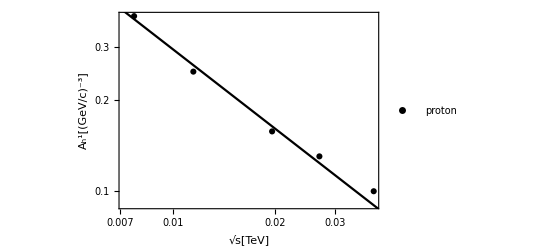

```mathematica
Show[{ListLogLogPlot[A1hsp,PlotStyle->Black,PlotLegends->Placed[{"proton"},{Right,Top}],PlotMarkers->Automatic],LogLogPlot[0.0052*sqs^-0.877,{sqs,0,0.1},PlotStyle->Black]},FrameLabel->{"√s[TeV]","A_h^1[(GeV/c)^-3]"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

```mathematica
Normal[NonlinearModelFit[A1hsp,A0h*sqs^-bh,{A0h,bh},sqs]]//TraditionalForm
```

0.00520714/sqs^0.877224

```mathematica
(*Xi*)
A1hXi={
N1[[1,;;]]/((Npart^1.35)),
N2[[1,;;]]/((Npart^1.35)),N3[[1,;;]]/((Npart^1.35)),N4[[1,;;]]/((Npart^1.35)),
N5[[1,;;]]/((Npart^1.35))};

A1hsXi={{7.7*^-3,Mean[A1hXi[[1]]]},
{11.5*^-3,Mean[A1hXi[[2]]]},
{19.6*^-3,Mean[A1hXi[[3]]]},
{27*^-3,Mean[A1hXi[[4]]]},
{39*^-3,Mean[A1hXi[[5]]]}};
Normal[NonlinearModelFit[A1hsXi,A0h*sqs^-bh,{A0h,bh},sqs]]//TraditionalForm
```

0.00233493/sqs^0.100133

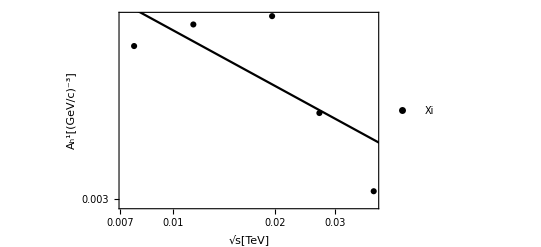

```mathematica
Show[{ListLogLogPlot[A1hsXi,PlotStyle->Black,PlotLegends->Placed[{"Xi"},{Right,Top}],PlotMarkers->Automatic],LogLogPlot[0.002335*sqs^-0.1001,{sqs,0,0.1},PlotStyle->Black]},FrameLabel->{"√s[TeV]","A_h^1[(GeV/c)^-3]"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

```mathematica
(*Lambda*)
A1hda={
N1[[2,;;]]/((Npart^1.35)),
N2[[2,;;]]/((Npart^1.35)),
N3[[2,;;]]/((Npart^1.35)),
N4[[2,;;]]/((Npart^1.35)),
N5[[2,;;]]/((Npart^1.35))};

A1hsda={{7.7*^-3,Mean[A1hda[[1]]]},
{11.5*^-3,Mean[A1hda[[2]]]},
{19.6*^-3,Mean[A1hda[[3]]]},
{27*^-3,Mean[A1hda[[4]]]},
{39*^-3,Mean[A1hda[[5]]]}};
Normal[NonlinearModelFit[A1hsda,A0h*sqs^-bh,{A0h,bh},sqs]]//TraditionalForm
```

0.00875283/sqs^0.443474

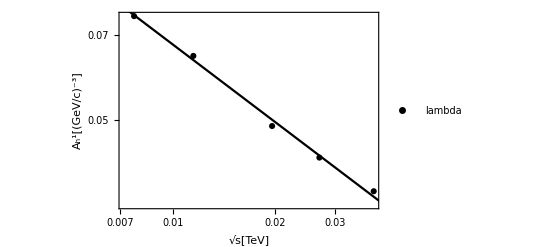

```mathematica
Show[{ListLogLogPlot[A1hsda,PlotStyle->Black,PlotLegends->Placed[{"lambda"},{Right,Top}],PlotMarkers->Automatic],LogLogPlot[0.008753*sqs^-0.4435,{sqs,0,0.1},PlotStyle->Black]},FrameLabel->{"√s[TeV]","A_h^1[(GeV/c)^-3]"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

```mathematica
(*phi*)
A1hphi={
N1[[4,;;]]/((Npart^0.9)),
N2[[4,;;]]/((Npart^0.9)),
N3[[4,;;]]/((Npart^0.9)),
N4[[4,;;]]/((Npart^0.9)),
N5[[4,;;]]/((Npart^0.9))};

A1hsphi={{7.7*^-3,Mean[A1hphi[[1]]]},
{11.5*^-3,Mean[A1hphi[[2]]]},
{19.6*^-3,Mean[A1hphi[[3]]]},
{27*^-3,Mean[A1hphi[[4]]]},
{39*^-3,Mean[A1hphi[[5]]]}};
Normal[NonlinearModelFit[A1hsphi,A0h*sqs^-bh,{A0h,bh},sqs]]//TraditionalForm
```

0.158612 sqs^0.338181

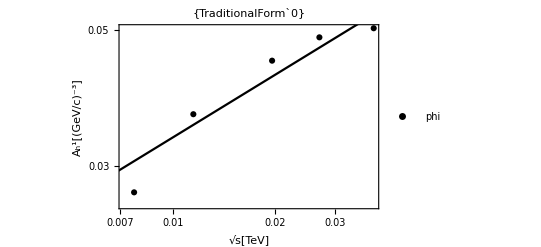

```mathematica
Show[{ListLogLogPlot[A1hsphi,PlotStyle->Black,PlotLegends->Placed[{"phi"},{Right,Top}],PlotMarkers->Automatic],LogLogPlot[0.158612*sqs^0.338181,{sqs,0,0.1},PlotStyle->Black]},FrameLabel->{"√s[TeV]","A_h^1[(GeV/c)^-3]"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick,PlotLabel->{"TraditionalForm`0"}]
```

```mathematica
(*39gev*)
Clear[AhNpart]
N5[[4,;;]];
AhNpart=Transpose[{%}];
For[i=1,i<5,i++,AhNpart=Insert[AhNpart,Npart[[i]],{i,1}]]
A5=AhNpart;
(*27gev*)
Clear[AhNpart]
N4[[4,;;]];
AhNpart=Transpose[{%}];
For[i=1,i<5,i++,AhNpart=Insert[AhNpart,Npart[[i]],{i,1}]]
A4=AhNpart;
(*19.6gev*)
Clear[AhNpart]
N3[[4,;;]];
AhNpart=Transpose[{%}];
For[i=1,i<5,i++,AhNpart=Insert[AhNpart,Npart[[i]],{i,1}]]
A3=AhNpart;
(*11.5gev*)
Clear[AhNpart]
N2[[4,;;]];
AhNpart=Transpose[{%}];
For[i=1,i<5,i++,AhNpart=Insert[AhNpart,Npart[[i]],{i,1}]]
A2=AhNpart;
(*7.7gev*)
Clear[AhNpart]
N1[[4,;;]];
AhNpart=Transpose[{%}];
For[i=1,i<5,i++,AhNpart=Insert[AhNpart,Npart[[i]],{i,1}]]
A1=AhNpart;
```

```mathematica
Normal[NonlinearModelFit[AhNpart,A1*x^ah,{A1,ah},x]]//TraditionalForm
```

0.0253316 x^1.03131

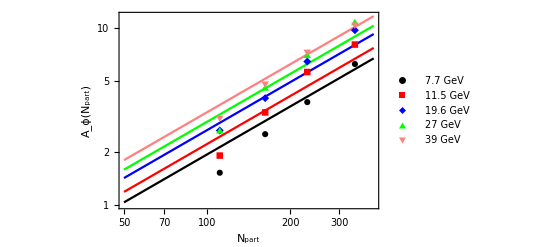

```mathematica
Show[{LogLogPlot[{0.158612*(7.7*^-3)^0.338181*x^0.9,0.158612*(11.5*^-3)^0.338181*x^0.9,0.158612*(19.6*^-3)^0.338181*x^0.9,0.158612*(27*^-3)^0.338181*x^0.9,0.158612*(39*^-3)^0.338181*x^0.9},{x,50,400},PlotStyle->{Black,Red,Blue,Green,Pink}],ListLogLogPlot[{A1,A2,A3,A4,A5},PlotLegends->Placed[{"7.7 GeV","11.5 GeV","19.6 GeV","27 GeV","39 GeV"},Right],PlotMarkers->Automatic,PlotStyle->{Black,Red,Blue,Green,Pink}]},FrameLabel->{"N_part","A_ϕ(N_part)"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

```mathematica
(*Omega*)
A1hOmega={
N3[[5,;;]]/((Npart^1.35)),
N4[[5,;;]]/((Npart^1.35)),
N5[[5,;;]]/((Npart^1.35))};

A1hsOmega={
{19.6*^-3,Mean[A1hOmega[[1]]]},
{27*^-3,Mean[A1hOmega[[2]]]},
{39*^-3,Mean[A1hOmega[[3]]]}};
Normal[NonlinearModelFit[A1hs,A0h*sqs^-bh,{A0h,bh},sqs]]//TraditionalForm
```

NonlinearModelFit::fitd: NonlinearModelFit 中的第一个参数 A1hs 不是一个列表，也不是一个矩形数组.

NonlinearModelFit[A1hs,A0h sqs^-bh,{A0h,bh},sqs]

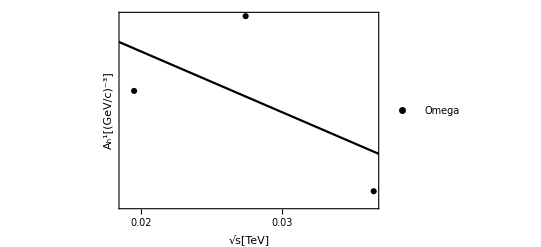

```mathematica
Show[{ListLogLogPlot[A1hsOmega,PlotStyle->Black,PlotLegends->Placed[{"Omega"},{Right,Top}],PlotMarkers->Automatic],LogLogPlot[0.000176345*sqs^-0.04959,{sqs,0,0.1},PlotStyle->Black]},FrameLabel->{"√s[TeV]","A_h^1[(GeV/c)^-3]"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

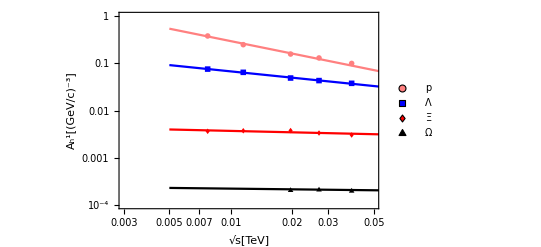

```mathematica
Show[{ListLogLogPlot[{A1hsp,A1hsda,A1hsXi,A1hsOmega},PlotStyle->Black,PlotLegends->Placed[{"p","Λ","Ξ","Ω"},{Left,Top}],PlotMarkers->{{Graphics[{Pink,Disk[]}],0.04},{Graphics[{Blue,Rectangle[]}],0.04},{Graphics[{Red,Parallelogram[{0,0},{{0.75,1},{-0.75,1}}]}],0.05},{Graphics[{Black,RegularPolygon[3]}],0.04}},PlotRange->{{0.003,0.05},{10^-4,1}}],
LogLogPlot[0.000176345*sqs^-0.04959,{sqs,0.005,0.15},PlotStyle->Black],LogLogPlot[0.008753*sqs^-0.4435,{sqs,0.005,0.15},PlotStyle->Blue],LogLogPlot[0.002335*sqs^-0.1001,{sqs,0.005,0.15},PlotStyle->Red],LogLogPlot[0.0052*sqs^-0.877,{sqs,0.005,0.15},PlotStyle->Pink]},FrameLabel->{"√s[TeV]","A_h^1[(GeV/c)^-3]"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

```mathematica
Export[%,"pic7.png"]
```

```mathematica
A1Xi=Table[{Npart[[i]],N1[[1,i]]},{i,1,4}];
A1da=Table[{Npart[[i]],N1[[2,i]]},{i,1,4}];
A1p=Table[{Npart[[i]],N1[[3,i]]},{i,1,4}];
A1Omega=Table[{Npart[[i]],N1[[5,i]]},{i,1,4}];
```

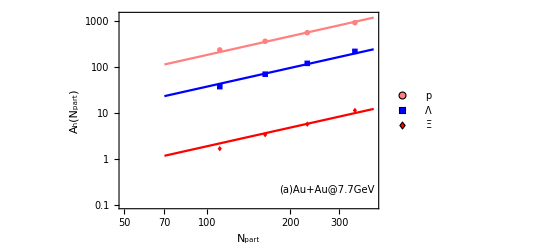

```mathematica
Show[{ListLogLogPlot[{A1p,A1da,A1Xi},PlotStyle->Black,PlotLegends->Placed[{"p","Λ","Ξ"},{Left,Top}],PlotMarkers->{{Graphics[{Pink,Disk[]}],0.04},{Graphics[{Blue,Rectangle[]}],0.04},{Graphics[{Red,Parallelogram[{0,0},{{0.75,1},{-0.75,1}}]}],0.05},{Graphics[{Black,RegularPolygon[3]}],0.04}},PlotRange->{{50,400},{0.1,1300}}],LogLogPlot[0.008753*(7.7*^-3)^-0.4435*n^1.35,{n,70,400},PlotStyle->Blue],LogLogPlot[0.002335*(7.7*^-3)^-0.1001*n^1.35,{n,70,400},PlotStyle->Red],LogLogPlot[0.0052*(7.7*^-3)^-0.877*n^1.35,{n,70,400},PlotStyle->Pink],Graphics[Text[Style["(a)Au+Au@7.7GeV",Italic,10,Black],Scaled[{0.8,0.1}]]]},
FrameLabel->{"N_part","A_h(N_part)"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

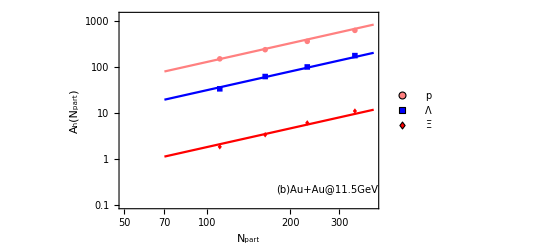

```mathematica
A1Xi=Table[{Npart[[i]],N2[[1,i]]},{i,1,4}];
A1da=Table[{Npart[[i]],N2[[2,i]]},{i,1,4}];
A1p=Table[{Npart[[i]],N2[[3,i]]},{i,1,4}];
A1Omega=Table[{Npart[[i]],N2[[5,i]]},{i,1,4}];
Show[{ListLogLogPlot[{A1p,A1da,A1Xi},PlotStyle->Black,PlotLegends->Placed[{"p","Λ","Ξ"},{Left,Top}],PlotMarkers->{{Graphics[{Pink,Disk[]}],0.04},{Graphics[{Blue,Rectangle[]}],0.04},{Graphics[{Red,Parallelogram[{0,0},{{0.75,1},{-0.75,1}}]}],0.05},{Graphics[{Black,RegularPolygon[3]}],0.04}},PlotRange->{{50,400},{0.1,1300}}],LogLogPlot[0.008753*(11.5*^-3)^-0.4435*n^1.35,{n,70,400},PlotStyle->Blue],LogLogPlot[0.002335*(11.5*^-3)^-0.1001*n^1.35,{n,70,400},PlotStyle->Red],LogLogPlot[0.0052*(11.5*^-3)^-0.877*n^1.35,{n,70,400},PlotStyle->Pink],Graphics[Text[Style["(b)Au+Au@11.5GeV",Italic,10,Black],Scaled[{0.8,0.1}]]]},
FrameLabel->{"N_part","A_h(N_part)"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

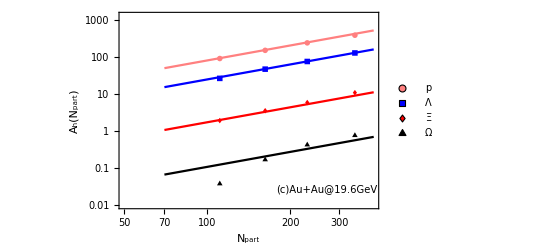

```mathematica
A1Xi=Table[{Npart[[i]],N3[[1,i]]},{i,1,4}];
A1da=Table[{Npart[[i]],N3[[2,i]]},{i,1,4}];
A1p=Table[{Npart[[i]],N3[[3,i]]},{i,1,4}];
A1Omega=Table[{Npart[[i]],N3[[5,i]]},{i,1,4}];
Show[{ListLogLogPlot[{A1p,A1da,A1Xi,A1Omega},PlotStyle->Black,PlotLegends->Placed[{"p","Λ","Ξ","Ω"},{Left,Top}],PlotMarkers->{{Graphics[{Pink,Disk[]}],0.04},{Graphics[{Blue,Rectangle[]}],0.04},{Graphics[{Red,Parallelogram[{0,0},{{0.75,1},{-0.75,1}}]}],0.05},{Graphics[{Black,RegularPolygon[3]}],0.04}},PlotRange->{{50,400},{0.01,1300}}],
LogLogPlot[0.008753*(19.6*^-3)^-0.4435*n^1.35,{n,70,400},PlotStyle->Blue],LogLogPlot[0.000176345*(19.6*^-3)^-0.04959*n^1.35,{n,70,400},PlotStyle->Black],LogLogPlot[0.002335*(19.6*^-3)^-0.1001*n^1.35,{n,70,400},PlotStyle->Red],LogLogPlot[0.0052*(19.6*^-3)^-0.877*n^1.35,{n,70,400},PlotStyle->Pink],Graphics[Text[Style["(c)Au+Au@19.6GeV",Italic,10,Black],Scaled[{0.8,0.1}]]]},
FrameLabel->{"N_part","A_h(N_part)"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

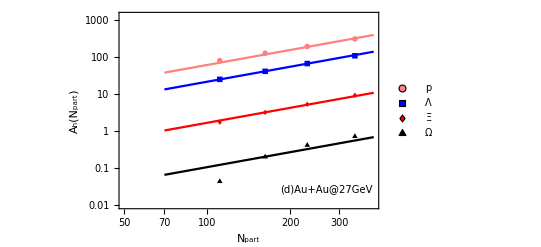

```mathematica
A1Xi=Table[{Npart[[i]],N4[[1,i]]},{i,1,4}];
A1da=Table[{Npart[[i]],N4[[2,i]]},{i,1,4}];
A1p=Table[{Npart[[i]],N4[[3,i]]},{i,1,4}];
A1Omega=Table[{Npart[[i]],N4[[5,i]]},{i,1,4}];
Show[{ListLogLogPlot[{A1p,A1da,A1Xi,A1Omega},PlotStyle->Black,PlotLegends->Placed[{"p","Λ","Ξ","Ω"},{Left,Top}],PlotMarkers->{{Graphics[{Pink,Disk[]}],0.04},{Graphics[{Blue,Rectangle[]}],0.04},{Graphics[{Red,Parallelogram[{0,0},{{0.75,1},{-0.75,1}}]}],0.05},{Graphics[{Black,RegularPolygon[3]}],0.04}},PlotRange->{{50,400},{0.01,1300}}],
LogLogPlot[0.008753*(27*^-3)^-0.4435*n^1.35,{n,70,400},PlotStyle->Blue],LogLogPlot[0.000176345*(27*^-3)^-0.04959*n^1.35,{n,70,400},PlotStyle->Black],LogLogPlot[0.002335*(27*^-3)^-0.1001*n^1.35,{n,70,400},PlotStyle->Red],LogLogPlot[0.0052*(27*^-3)^-0.877*n^1.35,{n,70,400},PlotStyle->Pink],Graphics[Text[Style["(d)Au+Au@27GeV",Italic,10,Black],Scaled[{0.8,0.1}]]]},
FrameLabel->{"N_part","A_h(N_part)"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

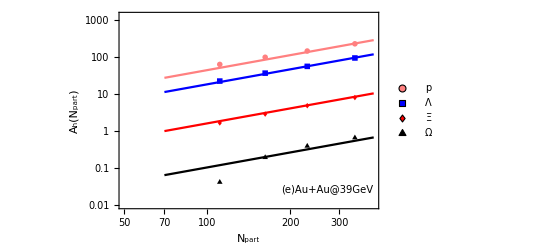

```mathematica
A1Xi=Table[{Npart[[i]],N5[[1,i]]},{i,1,4}];
A1da=Table[{Npart[[i]],N5[[2,i]]},{i,1,4}];
A1p=Table[{Npart[[i]],N5[[3,i]]},{i,1,4}];
A1Omega=Table[{Npart[[i]],N5[[5,i]]},{i,1,4}];
Show[{ListLogLogPlot[{A1p,A1da,A1Xi,A1Omega},PlotStyle->Black,PlotLegends->Placed[{"p","Λ","Ξ","Ω"},{Left,Top}],PlotMarkers->{{Graphics[{Pink,Disk[]}],0.04},{Graphics[{Blue,Rectangle[]}],0.04},{Graphics[{Red,Parallelogram[{0,0},{{0.75,1},{-0.75,1}}]}],0.05},{Graphics[{Black,RegularPolygon[3]}],0.04}},PlotRange->{{50,400},{0.01,1300}}],
LogLogPlot[0.008753*(39*^-3)^-0.4435*n^1.35,{n,70,400},PlotStyle->Blue],LogLogPlot[0.000176345*(39*^-3)^-0.04959*n^1.35,{n,70,400},PlotStyle->Black],LogLogPlot[0.002335*(39*^-3)^-0.1001*n^1.35,{n,70,400},PlotStyle->Red],LogLogPlot[0.0052*(39*^-3)^-0.877*n^1.35,{n,70,400},PlotStyle->Pink],Graphics[Text[Style["(e)Au+Au@39GeV",Italic,10,Black],Scaled[{0.8,0.1}]]]},
FrameLabel->{"N_part","A_h(N_part)"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```